```mathematica
img=ExampleData[{"TestImage","Lena"}]
```

```mathematica
dim={0,#}&/@ImageDimensions[img]
```

{{0,512},{0,512}}

```mathematica
rreals=(RandomReal/@dim)&/@Range[5000];
```

```mathematica
(*rreals={RandomVariate[NormalDistribution[648,160]],RandomReal[dim[[2]]]}&/@Range[2000];*)
```

```mathematica
vm=VoronoiMesh[Join[rreals,Tuples[dim]]];
```

```mathematica
colours=Map[Mean[#]&/@Transpose[PixelValue[img,Select[Tuples[{Range[Max[Ceiling[#[[1,1]]],dim[[1,1]]],Min[Floor[#[[1,2]]],dim[[1,2]]]],Range[Max[Ceiling[#[[2,1]]],dim[[2,1]]],Min[Floor[#[[2,2]]],dim[[2,2]]]]}&[MinMax/@Transpose[#/.Polygon[a_]->a]]],RegionMember[#]]]]&,MeshPrimitives[vm,2]];
```

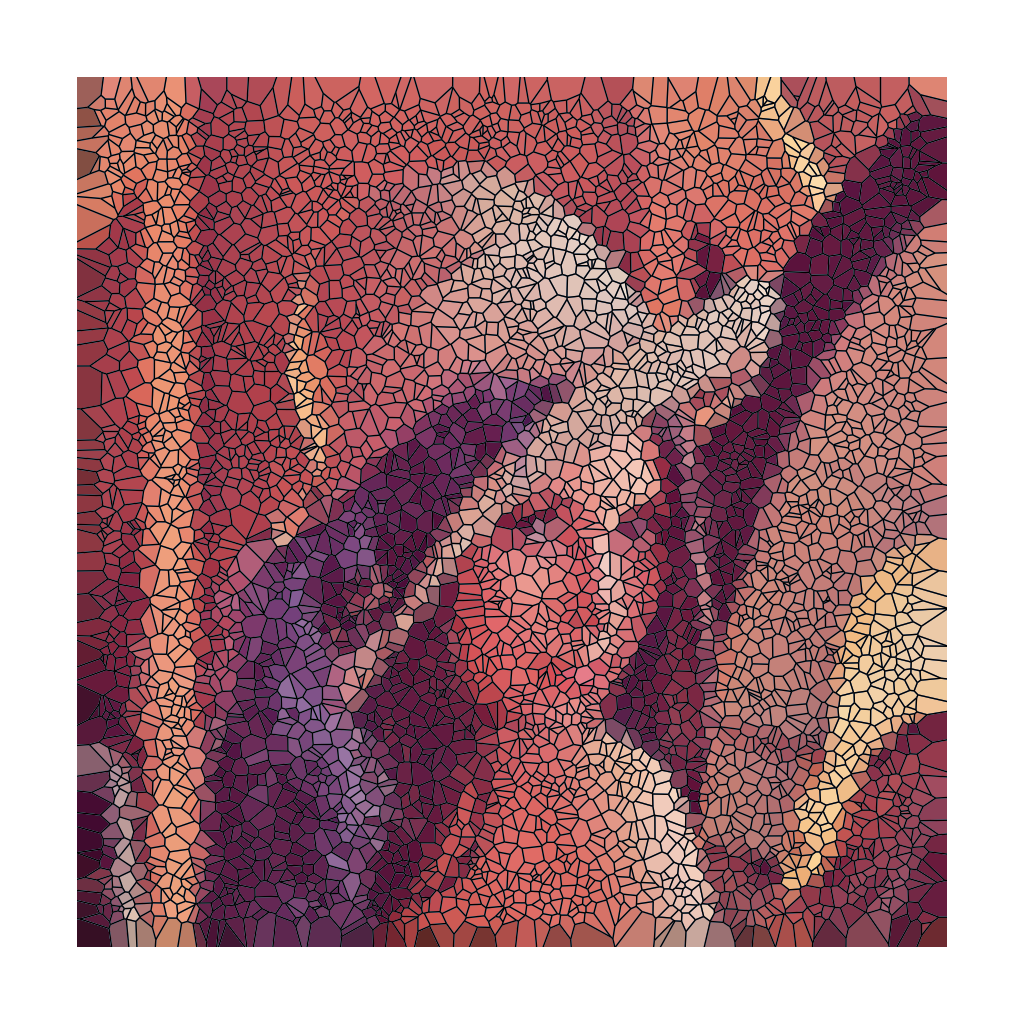

```mathematica
Show[ListPlot[dim,Axes->False,PlotRange->dim,AspectRatio->1],VoronoiMesh[Join[rreals,Tuples[dim]],MeshCellStyle->Append[MapIndexed[{2,#2[[1]]}->RGBColor@@#&,colours],{1,All}->{AbsoluteThickness[1],Black}]],ImageSize->{1024,1024}]
```

```mathematica
Export["Voronoi.png",%,ImageSize->{1024,1024}]
```

Voronoi.png